```mathematica
dir=FileNameJoin[{FileNameTake[NotebookDirectory[],{1,-2}],"TestFiles"}]
```

/Users/john/src/chaos/TestFiles

```mathematica
f=First@FileNames[__~~"C7L"~~__~~".cdf",dir<>"/tmp"]
```

/Users/john/src/chaos/TestFiles/tmp/SW_OPER_MAGAC7L_2__20220309T000000_20220309T235959_0101.cdf

```mathematica
binput=First@FileNames[__~~"LR"~~__~~".cdf",dir]
```

/Users/john/src/chaos/TestFiles/SW_OPER_MAGA_LR_1B_20220309T000000_20220309T235959_0506_MDR_MAG_LR.cdf

```mathematica
Needs["NasaCdf`"]
```

```mathematica
readNasaCdf[f,"Variables"]
```

{Timestamp,Latitude,Longitude,Radius,B_core_nec,B_crust_nec,dB_nec}

```mathematica
readNasaCdf[f,"Variable Attributes"]
```

{Timestamp→{FIELDNAM→Timestamp,CATDESC→ ,TYPE→CDF_EPOCH,UNITS→ ,VAR_TYPE→data,DEPEND_0→N/A,DISPLAY_TYPE→N/A,LABLAXIS→Timestamp,VALIDMIN→6.3814×10^13,VALIDMAX→6.38141×10^13,FORMAT→%f,TIME_BASE→AD0},Latitude→{FIELDNAM→Latitude,CATDESC→Geocentric latitude.,TYPE→CDF_REAL8,UNITS→degrees,VAR_TYPE→data,DEPEND_0→Timestamp,DISPLAY_TYPE→time_series,LABLAXIS→Latitude,VALIDMIN→-90.,VALIDMAX→90.,FORMAT→%5.1f,TIME_BASE→N/A},Longitude→{FIELDNAM→Longitude,CATDESC→Geocentric longitude.,TYPE→CDF_REAL8,UNITS→degrees,VAR_TYPE→data,DEPEND_0→Timestamp,DISPLAY_TYPE→time_series,LABLAXIS→Longitude,VALIDMIN→-180.,VALIDMAX→180.,FORMAT→%6.1f,TIME_BASE→N/A},Radius→{FIELDNAM→Radius,CATDESC→Geocentric radius.,TYPE→CDF_REAL8,UNITS→m,VAR_TYPE→data,DEPEND_0→Timestamp,DISPLAY_TYPE→time_series,LABLAXIS→Radius,VALIDMIN→6.4×10^6,VALIDMAX→7.4×10^6,FORMAT→%9.1f,TIME_BASE→N/A},B_core_nec→{FIELDNAM→B_core_nec,CATDESC→CHAOS 7 core magnetic field (interpolated),TYPE→CDF_REAL8,UNITS→nT,VAR_TYPE→data,DEPEND_0→Timestamp,DISPLAY_TYPE→time_series,LABLAXIS→B_core_nec,VALIDMIN→-70000.,VALIDMAX→70000.,FORMAT→%8.1f,TIME_BASE→N/A},B_crust_nec→{FIELDNAM→B_crust_nec,CATDESC→CHAOS 7 crustal magnetic field (interpolated),TYPE→CDF_REAL8,UNITS→nT,VAR_TYPE→data,DEPEND_0→Timestamp,DISPLAY_TYPE→time_series,LABLAXIS→B_crust_nec,VALIDMIN→-1000.,VALIDMAX→1000.,FORMAT→%8.2f,TIME_BASE→N/A},dB_nec→{FIELDNAM→dB_nec,CATDESC→Residual magnetic field from Swarm MAG with respect to CHAOS 7 core plus crustal field.,TYPE→CDF_REAL8,UNITS→nT,VAR_TYPE→data,DEPEND_0→Timestamp,DISPLAY_TYPE→time_series,LABLAXIS→dB_nec,VALIDMIN→5000.,VALIDMAX→5000.,FORMAT→%8.2f,TIME_BASE→N/A}}

```mathematica
data=readNasaCdf[f,"Data"];
```

```mathematica
bin=readNasaCdf[binput,"Data"];
```

```mathematica
Import[binput,"Elements"]
```

{Annotations,Data,DataEncoding,DataFormat,Datasets,Metadata}

```mathematica
Import[binput,"Annotations"]
```

{{DESCRIPTION→Time stamp,UNITS→-},{DESCRIPTION→Synchronization status,UNITS→-},{DESCRIPTION→Position in ITRF - Latitude,UNITS→deg},{DESCRIPTION→Position in ITRF - Longitude,UNITS→deg},{DESCRIPTION→Position in ITRF - Radius,UNITS→m},{DESCRIPTION→Magnetic field intensity,UNITS→nT},{DESCRIPTION→Magnetic stray field correction intensity of AOCS magneto-torquer coils,UNITS→nT},{DESCRIPTION→Magnetic stray field correction intensity of all other sources,UNITS→nT},{DESCRIPTION→Error estimate on magnetic field intensity,UNITS→nT},{DESCRIPTION→Magnetic field vector, VFM frame,UNITS→nT},{DESCRIPTION→Magnetic field vector, NEC frame,UNITS→nT},{DESCRIPTION→Magnetic stray field correction vector of Sun induced perturbation, VFM frame,UNITS→nT},{DESCRIPTION→Magnetic stray field correction vector of AOCS magneto-torquer coils, VFM frame,UNITS→nT},{DESCRIPTION→Magnetic stray field correction vector of all other sources, VFM frame,UNITS→nT},{DESCRIPTION→Error estimates on magnetic field, VFM frame,UNITS→nT},{DESCRIPTION→Quaternion, transformation: NEC - CRF,UNITS→-},{DESCRIPTION→Error estimates on attitude information,UNITS→mdeg},{DESCRIPTION→Flags characterizing the magnetic field intensity measurement (F),UNITS→-},{DESCRIPTION→Flags characterizing the magnetic field measurement,UNITS→-},{DESCRIPTION→Flags characterizing the attitude information,UNITS→-},{DESCRIPTION→Flags characterizing the S/C platform information,UNITS→-},{DESCRIPTION→ASM frequency calibration data deviation,UNITS→-}}

```mathematica
data[[5]]
```

{3.85577×10^9,75.7514,-96.0258,6.79338×10^6,{2609.01,-573.87,47443.7},{-2.60568,-0.217721,-1.74737},{-62.7656,-121.484,11.5915}}

```mathematica
time=data[[All,1]];
lat=data[[All,2]];
lon=data[[All,3]];
rad=data[[All,4]];
core=data[[All,5]];
crust=data[[All,6]];
dbmeas=data[[All,7]];
```

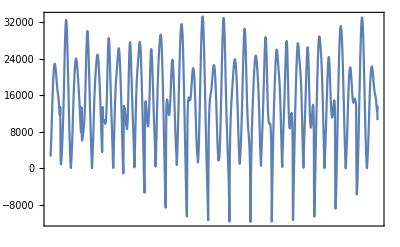

```mathematica
DateListPlot[deleteRedundantPoints[Transpose[{time,core[[All,1]]}],1000]]
```

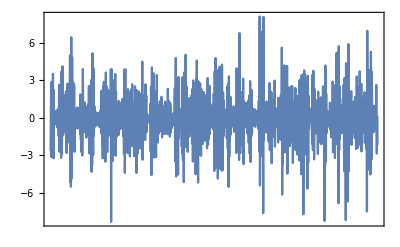

```mathematica
DateListPlot[deleteRedundantPoints[Transpose[{time,crust[[All,1]]}],1000],PlotRange->All]
```

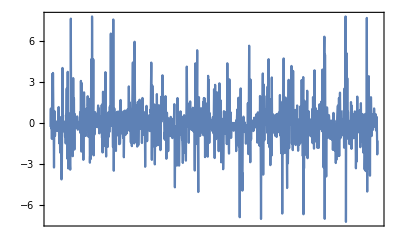

```mathematica
DateListPlot[deleteRedundantPoints[Transpose[{time,crust[[All,2]]}],1000],PlotRange->All]
```

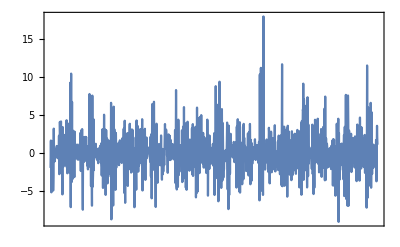

```mathematica
DateListPlot[deleteRedundantPoints[Transpose[{time,crust[[All,3]]}],1000],PlotRange->All]
```

```mathematica
StandardDeviation/@Transpose[core]
```

{9177.05,4932.22,33885.8}

```mathematica
StandardDeviation/@Transpose[crust]
```

{1.64238,1.48372,2.28842}

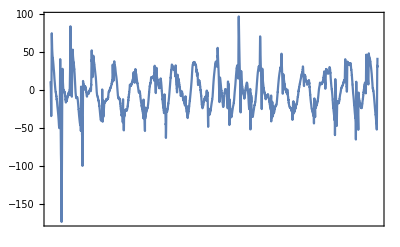

```mathematica
DateListPlot[deleteRedundantPoints[Transpose[{time,dbmeas[[All,3]]}],1000],PlotRange->All]
```

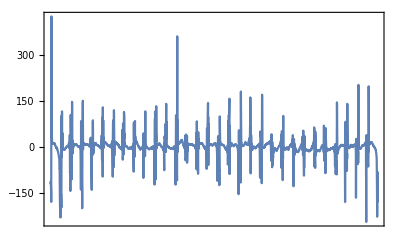

```mathematica
DateListPlot[deleteRedundantPoints[Transpose[{time,dbmeas[[All,2]]}],1000],PlotRange->All]
```

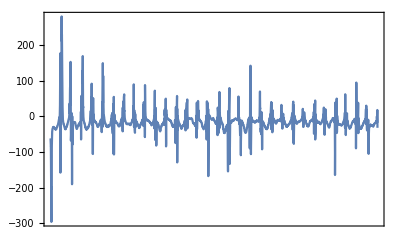

```mathematica
DateListPlot[deleteRedundantPoints[Transpose[{time,dbmeas[[All,1]]}],1000],PlotRange->All]
```

```mathematica
ind=1;;3000;
```

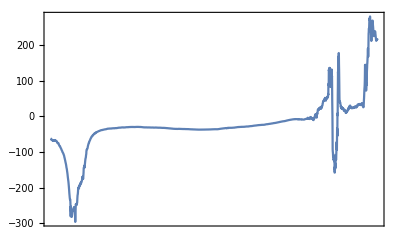

```mathematica
DateListPlot[Transpose[{time[[ind]],dbmeas[[ind,1]]}],PlotRange->All]
```

```mathematica
ind=650;;3000;
```

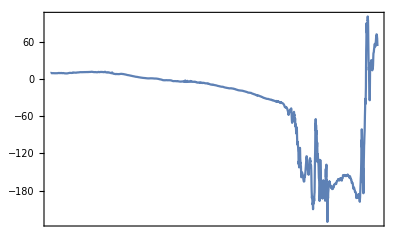

```mathematica
DateListPlot[Transpose[{time[[ind]],dbmeas[[ind,2]]}],PlotRange->All]
```

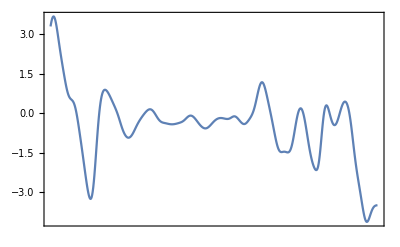

```mathematica
DateListPlot[Transpose[{time[[ind]],crust[[ind,2]]}],PlotRange->All]
```

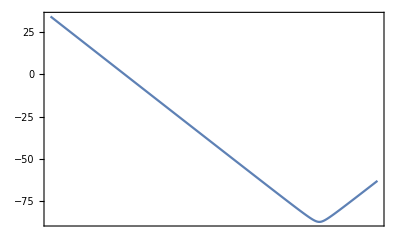

```mathematica
DateListPlot[Transpose[{time[[ind]],lat[[ind]]}],PlotRange->All]
```

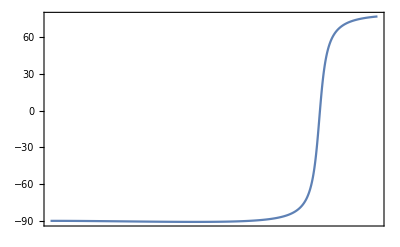

```mathematica
DateListPlot[Transpose[{time[[ind]],lon[[ind]]}],PlotRange->All]
```

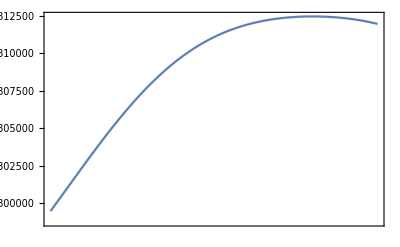

```mathematica
DateListPlot[Transpose[{time[[ind]],rad[[ind]]}],PlotRange->All]
```

```mathematica
DateList@time[[ind]][[1]]
```

{2022,3,9,0,10,49.}

```mathematica
DateDifference[{2022},time[[ind]][[1]]]
```

67.0075 days

```mathematica
fr=2022+67.0075/365.25
```

2022.18

```mathematica
2022.1834565366187
```

```mathematica
crust[[1]]
```

{-2.59836,-0.202461,-1.95024}

This is the same output as the matlab CHAOS example, to two decimal places, modified to show crustal model, which uses the order 6 BSpline. Validates crustal field implemented correctly.

```mathematica
readNasaCdf[binput,"Variables"]
```

{Timestamp,SyncStatus,Latitude,Longitude,Radius,F,dF_AOCS,dF_other,F_error,B_VFM,B_NEC,dB_Sun,dB_AOCS,dB_other,B_error,q_NEC_CRF,Att_error,Flags_F,Flags_B,Flags_q,Flags_Platform,ASM_Freq_Dev}

```mathematica
bin[[1]]
```

{3.85577×10^9,0,76.0051,-96.2096,6.79336×10^6,0.,0.1575,-0.0134,0.,{45550.4,2568.62,13290.},{2483.36,-691.841,47449.1},{0.7156,0.3889,1.6205},{-0.3316,0.0113,1.635},{-0.1884,0.0137,-0.0436},{0.2138,0.2153,0.3116},{-0.00325244,-0.000321896,-0.995969,0.0896356},1.1492,255,8,0,1,0.}

```mathematica
DateDifference[{2000},time[[1]]]
```

8103 days

```mathematica
90-76.0051
```

13.9949

```mathematica
alt=bin[[1,5]]/1000.-6371.2
```

422.158